```mathematica
ClearAll["Global`*"]
```

```mathematica
IP[ts_,λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_] :=ItoProcess[{
ⅆF[t]== ts*((λ*F[t]-σ*(1-R[t])*F[t] + ρ*R[t]*H[t])ⅆt ),
ⅆH[t]== ts*((σ*(1-R[t])*F[t] - ρ*R[t]*H[t] - μ*H[t])ⅆt) ,
ⅆR[t]==ts*((α*ⅆt+ϵ*ⅆW[t])*R[t]*(1-R[t]) - R[t]*(ρ*H[t] + β*F[t])ⅆt)},
{F[t],H[t],R[t]},
{{F,H,R},{F0,H0,R0}},
t,
W\[Distributed]WienerProcess[]
]
```

```mathematica
stochsol[T_,TSlice_,Iterations_,ts_, λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_]:=RandomFunction[IP[ts, λ,σ,ρ,μ,α,β,ϵ,F0,H0,R0],{0,T,TSlice},Iterations,Method->"KloedenPlatenSchurz"];
TD = With[{
T=500,
TSlice=0.1,
Iterations=1,
ts=1,
λ=0.2,
σ=0.22,
ρ=0.4,
μ=0.3,
α=0.5,
β=0.2,
ϵ=0.2},
Table[stochsol[T,TSlice,Iterations,ts,λ,σ,ρ,μ,α,β,ϵ,RandomReal[{0.2,1}],RandomReal[{0.2,1}],RandomReal[{0.2,1}]]["PathComponents"],{5}]
];
```

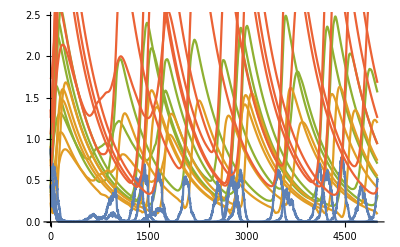

```mathematica
Show[{
Table[ListLinePlot[TD[[i]][[1]][[2]][[1]][[1]],PlotRange->All,PlotStyle->ColorData[97,3]],{i,1,5,1}],
Table[ListLinePlot[TD[[i]][[2]][[2]][[1]][[1]],PlotRange->All,PlotStyle->ColorData[97,2]],{i,1,5,1}],
Table[ListLinePlot[TD[[i]][[3]][[2]][[1]][[1]],PlotRange->All,PlotStyle->ColorData[97,1]],{i,1,5,1}],
Table[ListLinePlot[TD[[i]][[1]][[2]][[1]][[1]]+TD[[i]][[2]][[2]][[1]][[1]],PlotRange->All,PlotStyle->ColorData[97,4]],{i,1,5,1}]
}]
```

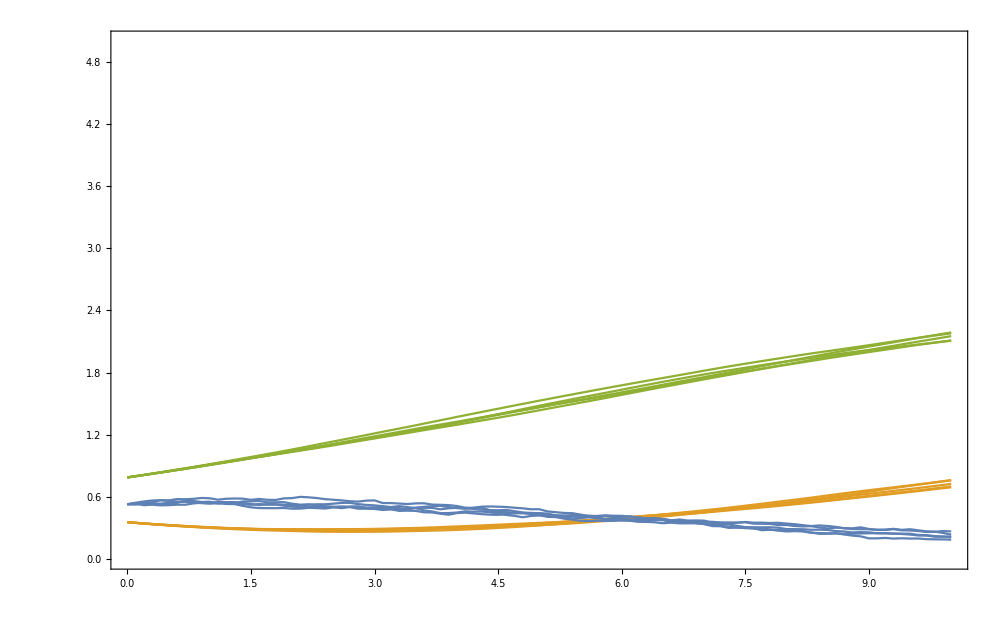

```mathematica
Show[{Table[ListLinePlot[TD[[i]],PlotStyle->ColorData[97,4-i],PlotRange->{0,5},Frame->True],{i,1,3}]}]
```

```mathematica
TD[[1]][[2]][[1]][[5]]+TD[[2]][[2]][[1]][[5]]
```

```mathematica
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
IPSigma[ts_,λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_] :=ItoProcess[{
ⅆF[t]== ts*((λ*F[t]-σ*(1-R[t])*F[t] + ρ*R[t]*H[t])ⅆt ),
ⅆH[t]== ts*((σ*(1-R[t])*F[t] - ρ*R[t]*H[t] - μ*H[t])ⅆt) ,
ⅆR[t]==ts*((α*ⅆt+ϵ*ⅆW[t])*R[t]*(1-R[t]) - R[t]*(ρ*H[t] + β*F[t])ⅆt)},
{F[t],H[t],R[t]},
{{F,H,R},{F0,H0,R0}},
t,
W\[Distributed]WienerProcess[]
];
stochsol[T_,TSlice_,Iterations_,ts_, λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_]:=RandomFunction[IPSigma[ ts,λ,σ,ρ,μ,α,β,ϵ,F0,H0,R0],{0,T,TSlice},Iterations,Method->"KloedenPlatenSchurz"];
(*sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,53}];*)
sigvalues =Table[x,{x,0.21,4.21,0.2}];
ExtinctSigma=ParallelTable[
With[{
T=100,
TSlice=0.1,
Iterations=1,
ts=1,
λ=0.2,
σ=sigma,
ρ=0.4,
μ=0.3,
α=0.5,
β=0.2,
ϵ=0.2,
Its=500},
TD =Table[stochsol[T,TSlice,Iterations,ts,λ,σ,ρ,μ,α,β,ϵ,RandomReal[{0.2,1}],RandomReal[{0.2,1}],RandomReal[{0.2,1}]]["PathComponents"],{Its}];
Extinct=Table[
consumerdensity=TD[[it]][[1]][[2]][[1]][[1]]+TD[[it]][[2]][[2]][[1]][[1]];
TestThreshold[consumerdensity,0.1*Mean[consumerdensity]],
{it,1,Its,1}];
{N[sigma/ρ],N[Total[Extinct]/Its]}
],
{sigma,sigvalues}];
```

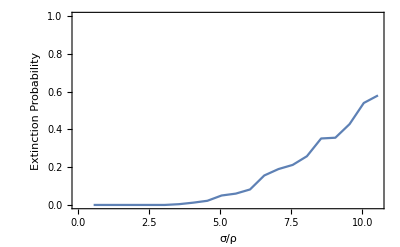

```mathematica
TroughPlot=ListLinePlot[ExtinctSigma,PlotRange->{0,1},Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Extinction.pdf",TroughPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Extinction.pdf

```mathematica
IPSigma[ts_,λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_] :=ItoProcess[{
ⅆF[t]== ts*((λ*F[t]-σ*(1-R[t])*F[t] + ρ*R[t]*H[t])ⅆt ),
ⅆH[t]== ts*((σ*(1-R[t])*F[t] - ρ*R[t]*H[t] - μ*H[t])ⅆt) ,
ⅆR[t]==ts*((α*ⅆt+ϵ*ⅆW[t])*R[t]*(1-R[t]) - R[t]*(ρ*H[t] + β*F[t])ⅆt)},
{F[t],H[t],R[t]},
{{F,H,R},{F0,H0,R0}},
t,
W\[Distributed]WienerProcess[]
];
stochsol[T_,TSlice_,Iterations_,ts_, λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_]:=RandomFunction[IPSigma[ ts,λ,σ,ρ,μ,α,β,ϵ,F0,H0,R0],{0,T,TSlice},Iterations,Method->"KloedenPlatenSchurz"];
```

```mathematica
With[{
T=500,
TSlice=0.1,
Iterations=1,
ts=1,
λ=0.2,
σ=0.22,
ρ=0.4,
μ=0.3,
α=0.5,
β=0.2,
ϵ=0.2,
Its=2},
TD =Table[stochsol[T,TSlice,Iterations,ts,λ,σ,ρ,μ,α,β,ϵ,RandomReal[{0.2,1}],RandomReal[{0.2,1}],RandomReal[{0.2,1}]]["PathComponents"],{Its}];
]
```